```mathematica
Clear[GRN2];
EnumTF[TF_,gene_,transcript_,ktx_]:=(
boundGene=Symbol[ToString[TF]<>ToString[gene]];
Seq[
revrxn[TF+gene,boundGene,kON,kOFF],
rxn[boundGene,boundGene+transcript,ktx]
]
)


Second[x_]:=x[[2]]

EnumConc[TF_,conc_]:=(
Cases[Tuples[{TF,conc}],{v_,v_[0]==b_}->{v,b}]
)

GRN2[IN_,OUT_,init_]:=(

active=First[#]&/@Select[IN,Second[#]=="ON" &];
repress=First[#]&/@Select[IN,Second[#]=="OFF"&];
With[{nodes= Complement[Join[active,repress],Cases[init,v_[0]== _ -> v]]}, inits=Join[init,(#[0]==0)& /@ nodes ]];
output=ToString[OUT];
gene=Symbol["g"<>output];
transcript=Symbol["t"<>output];
Seq[
Function[x,EnumTF[x,gene,transcript,kAct]]/@active,Function[x,EnumTF[x,gene,transcript,kRep]]/@repress,
rxn[gene,gene+transcript,ktx],
rxn[transcript,transcript+OUT,ktl],
rxn[transcript,0,krd],
rxn[OUT,0,kpd],


Function[x,conc[First[x],Second[x]]]/@EnumConc[Join[active,repress],inits],
conc[gene,Gtot]

]
)

GRN2[{{X,"ON"},{Y,"OFF"}},Z,{X[0]==1,Y[0]==1}]
```

Sequence[{A+gZ →^kON AgZ ,AgZ →^kOFF A+gZ ,AgZ →^kAct AgZ+tZ },{B+gZ →^kON BgZ ,BgZ →^kOFF B+gZ ,BgZ →^kRep BgZ+tZ },gZ →^ktx gZ+tZ ,tZ →^ktl tZ+Z ,tZ →^krd 0 ,Z →^kpd 0 ,{conc[A,1],conc[B,1]},conc[gZ,Gtot]]

```mathematica
Clear[GRNSim,GRNSimPlot];
GRNSim[GRN_,watch_,time_]:=(
rsys=Flatten[GRN];

sol=SimulateRxnsys[rsys/.{kON->1.0,kOFF->1.0,kAct->60.0,kRep->0.0 ,ktx->10.0,ktl->1.0,kpd->1.0,krd->5.0,kc->1000,Gtot->1},time];
(#[t]&/@watch)/.sol
)

GRNSimPlot[GRN_,watch_,time_]:=(
plotter=GRNSim[GRN,watch,time];
Plot[plotter,{t,0,time},PlotRange->All,
PlotLegends->watch]
)

tmax=20;

y=Table[{i,GRNSim[{GRN2[{{X,"ON"},{Y,"OFF"}},Z,{X[0]==i,Y[0]==5}]},{Z},tmax][[1]][[0]][tmax]},{i,0,10,0.5}];
y=ListPlot[y];
```

Sequence[B+A →^kc 0 ,{A+gZ →^kON AgZ ,AgZ →^kOFF A+gZ ,AgZ →^kAct AgZ+tZ },{B+gZ →^kON BgZ ,BgZ →^kOFF B+gZ ,BgZ →^kRep BgZ+tZ },gZ →^ktx gZ+tZ ,tZ →^ktl tZ+Z ,tZ →^krd 0 ,Z →^kpd 0 ,{conc[A,i],conc[B,5]},conc[gZ,Gtot]]

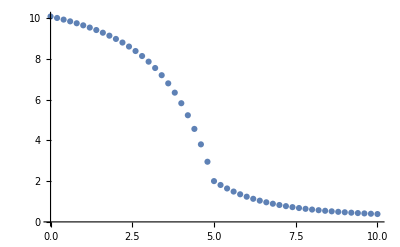

```mathematica
Clear[titrGRN2];
titrGRN2[GRN_,inits_]:=(
inputs=Flatten[GRN];
anyl=inputs[[1]];
titr=inputs[[2]];
OUT=inputs[[3]];
Seq[
rxn[titr+anyl,0,kc],

GRN2[{{titr,"OFF"},{anyl,"ON"}},OUT,inits]
]
)
titrGRN2[{{X,Y},Z},{X[0]==i,Y[0]==5}]
tmax=50;

Manipulate[GRNSimPlot[{titrGRN2[{{X,Y},Z},{X[0]==i,Y[0]==5}]},{X,Y,Z},tmax],{i,0,10}]
y=Table[{i,GRNSim[{titrGRN2[{{Y,X},Z},{X[0]==i,Y[0]==5}]},{Z},tmax][[1]][[0]][tmax]},{i,0,10,0.2}];
y=ListPlot[y]
```

```mathematica
{titrGRN2[{{X,Y},Z},{X[0]==i,Y[0]==5}],titrGRN2[{{U,Z},V},{U[0]==0,Z[0]==0}]}
```

{Y+X →^kc 0 ,{X+gZ →^kON XgZ ,XgZ →^kOFF X+gZ ,XgZ →^kAct XgZ+tZ },tZ →^1. tZ+Z ,tZ →^5. 0 ,Z →^1. 0 ,{conc[X,i],conc[Y,5]},conc[gZ,1],Z+U →^kc 0 ,{U+gV →^kON UgV ,UgV →^kOFF U+gV ,UgV →^kAct UgV+tV },tV →^1. tV+V ,tV →^5. 0 ,V →^1. 0 ,{conc[U,0],conc[Z,0]},conc[gV,1]}

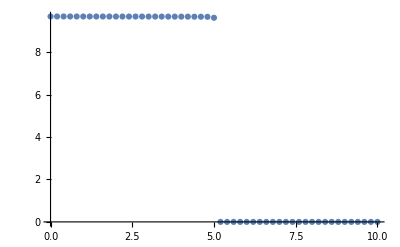

```mathematica
y=Table[{i,GRNSim[{titrGRN2[{{X,Y},Z},{X[0]==i,Y[0]==5}],titrGRN2[{{U,Z},V},{U[0]==5,Z[0]==0}]},{V},tmax][[1]][[0]][tmax]},{i,0,10,0.2}];
ListPlot[y]
```

{{Y+gYT →^kON YgYT ,YgYT →^kOFF Y+gYT ,YgYT →^kAct YgYT+tYT },{},gYT →^ktx gYT+tYT ,tYT →^ktl tYT+YT ,tYT →^krd 0 ,YT →^kpd 0 ,{conc[Y,5]},conc[gYT,Gtot],{X+gXA →^kON XgXA ,XgXA →^kOFF X+gXA ,XgXA →^kAct XgXA+tXA },{},gXA →^ktx gXA+tXA ,tXA →^ktl tXA+XA ,tXA →^krd 0 ,XA →^kpd 0 ,{conc[X,10]},conc[gXA,Gtot],Y+X →^kc 0 ,{XA+gZ →^kON XAgZ ,XAgZ →^kOFF XA+gZ ,XAgZ →^kAct XAgZ+tZ },{YT+gZ →^kON YTgZ ,YTgZ →^kOFF YT+gZ ,YTgZ →^kRep YTgZ+tZ },gZ →^ktx gZ+tZ ,tZ →^ktl tZ+Z ,tZ →^krd 0 ,Z →^kpd 0 ,{conc[XA,0],conc[YT,0]},conc[gZ,Gtot]}

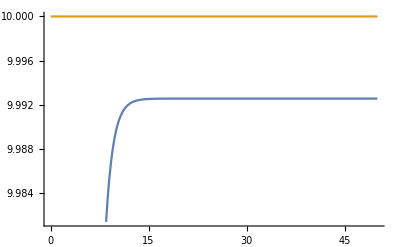

```mathematica
Clear[X,Y,Z];
titrGRN3[GRN_,inits_]:=(
inputs=Flatten[GRN];
anyl=inputs[[1]];
titr=inputs[[2]];
OUT=inputs[[3]];
titrOUT=Symbol[ToString[titr]<>"T"];
anylOUT=Symbol[ToString[anyl]<>"A"];
titrInits=Second[#]&/@Select[Cases[inits,v_[0]==b_->{v,v[0]==b}],First[#]==titr&];
anylInits=Second[#]&/@Select[Cases[inits,v_[0]==b_->{v,v[0]==b}],First[#]==anyl&];
Seq[
GRN2[{{titr,"ON"}},titrOUT,titrInits],
GRN2[{{anyl,"ON"}},anylOUT,anylInits],
rxn[titr+anyl,0,kc],

GRN2[{{titrOUT,"OFF"},{anylOUT,"ON"}},OUT,{titrOUT[0]==0,anylOUT[0]==0}]
]
)

sys={
titrGRN3[{{X,Y},Z},{X[0]==10,Y[0]==5}]
}
tmax=50;
sol=SimulateRxnsys[dummySys2,tmax];
plotter={Y[t]}/.sol;
Plot[{plotter,10},{t,0,50}]
```

```mathematica
Clear[GRNSim2,GRNSimPlot2];
GRNSim2[GRN_,watch_,time_]:=(
rsys=Flatten[GRN];

sol=SimulateRxnsys[rsys/.{kON->0.25,kOFF->0.25,kAct->50.0,kRep->40.0 ,ktx->0.0,ktl->1.0,kpd->1.0,krd->5.0,kc->1000,Gtot->1},time];
(#[t]&/@watch)/.sol
)
GRNSimPlot2[GRN_,watch_,time_]:=(
plotter=GRNSim2[GRN,watch,time];
Plot[plotter,{t,0,time},PlotRange->All,
PlotLegends->watch]
)


Clear[A,B,Z,INT];
NAND1[GRN_,inits_]:=(
inputs=Flatten[GRN];
X=inputs[[1]];
Y=inputs[[2]];
OUT=inputs[[3]];
INT=Symbol[ToString[OUT]<>"INT"];
titr=Symbol[ToString[OUT]<>"T"];
rsys={
{GRN2[{{X,"ON"}},INTX,inits]}/.{kON->0.25,kOFF->0.25,kAct->60.0},
{GRN2[{{Y,"ON"}},INTY,inits]}/.{kON->0.25,kOFF->0.25,kAct->60.0},
rxn[INTX+INTY,INT,kc],
rxn[INT,0,kpd],
conc[titr,5],
rxn[INT+titr,0,kc],

{GRN2[{{INT,"OFF"}},OUT,{INT[0]==0,titr[0]==0}]}/.{kON->2.0,kOFF->1.0,kRep->0.0,ktx->50.0}
}
)

NAND1[{{A,B},Z},{X[0]==0,Y[0]==0}]

tmax=50;
Manipulate[GRNSimPlot2[NAND1[{{A,B},Z},{A[0]==i,B[0]==j}],{A,B,Z,INT},tmax],{{i,1,"X"},0,10},{{j,1,"Y"},0,10}]
```

{{{A+gINTX →^0.25 AgINTX ,AgINTX →^0.25 A+gINTX ,AgINTX →^60. AgINTX+tINTX },{},gINTX →^ktx gINTX+tINTX ,tINTX →^ktl tINTX+INTX ,tINTX →^krd 0 ,INTX →^kpd 0 ,{conc[A,0]},conc[gINTX,Gtot]},{{B+gINTY →^0.25 BgINTY ,BgINTY →^0.25 B+gINTY ,BgINTY →^60. BgINTY+tINTY },{},gINTY →^ktx gINTY+tINTY ,tINTY →^ktl tINTY+INTY ,tINTY →^krd 0 ,INTY →^kpd 0 ,{conc[B,0]},conc[gINTY,Gtot]},INTX+INTY →^kc ZINT ,ZINT →^kpd 0 ,conc[ZT,5],ZINT+ZT →^kc 0 ,{{},{ZINT+gZ →^2. ZINTgZ ,ZINTgZ →^1. ZINT+gZ ,ZINTgZ →^0. ZINTgZ+tZ },gZ →^50. gZ+tZ ,tZ →^ktl tZ+Z ,tZ →^krd 0 ,Z →^kpd 0 ,{conc[ZINT,0]},conc[gZ,Gtot]}}

```mathematica
NAND1[GRN_,inits_]:=(
inputs=Flatten[GRN];
X=inputs[[1]];
Y=inputs[[2]];
OUT=inputs[[3]];
INT=Symbol[ToString[OUT]<>"INT"];
titr=Symbol[ToString[OUT]<>"T"];
rsys={
{GRN2[{{X,"ON"},{Y,"ON"}},INT,inits]}/.{kON->0.25,kOFF->0.25,kAct->60.0},
{GRN2[{{titr,"ON"}},titr,inits]}/.{kON->2.0,kOFF->1.0,kAct->81.0},
rxn[INT,0,kpd],
conc[titr,5],
rxn[INT+titr,0,kc],

{GRN2[{{INT,"OFF"}},OUT,{INT[0]==0,titr[0]==0}]}/.{kON->2.0,kOFF->1.0,kRep->0.0,ktx->50.0}
}
)

NAND1[{{A,B},Z},{X[0]==0,Y[0]==0}]

tmax=50;
Manipulate[GRNSimPlot2[NAND1[{{A,B},Z},{A[0]==i,B[0]==j}],{A,B,Z,INT,titr},tmax],{{i,1,"X"},0,10},{{j,1,"Y"},0,10}]
```

{{{A+gZINT →^0.25 AgZINT ,AgZINT →^0.25 A+gZINT ,AgZINT →^60. AgZINT+tZINT ,B+gZINT →^0.25 BgZINT ,BgZINT →^0.25 B+gZINT ,BgZINT →^60. BgZINT+tZINT },{},gZINT →^ktx gZINT+tZINT ,tZINT →^ktl tZINT+ZINT ,tZINT →^krd 0 ,ZINT →^kpd 0 ,{conc[A,0],conc[B,0]},conc[gZINT,Gtot]},{{ZT+gZT →^2. ZTgZT ,ZTgZT →^1. ZT+gZT ,ZTgZT →^81. ZTgZT+tZT },{},gZT →^ktx gZT+tZT ,tZT →^ktl tZT+ZT ,tZT →^krd 0 ,ZT →^kpd 0 ,{conc[ZT,0]},conc[gZT,Gtot]},ZINT →^kpd 0 ,conc[ZT,5],ZINT+ZT →^kc 0 ,{{},{ZINT+gZ →^2. ZINTgZ ,ZINTgZ →^1. ZINT+gZ ,ZINTgZ →^0. ZINTgZ+tZ },gZ →^50. gZ+tZ ,tZ →^ktl tZ+Z ,tZ →^krd 0 ,Z →^kpd 0 ,{conc[ZINT,0]},conc[gZ,Gtot]}}

Scratch Work

```mathematica
{X[0]==1,Y[0]==1}
(#[0]==_->#&)/@{X[0]==1,Y[0]==1}
Select[Cases[{X[0]==1,Y[0]==1},v_[0]==b_->{v,v[0]==b}],First[#]==Y&]
Second[#]&/@Select[Cases[{X[0]==1,Y[0]==1},v_[0]==b_->{v,v[0]==b}],First[#]==Y&]
```

{X[0]==1,Y[0]==1}

{(X[0]==1)[0]==_→X[0]==1,(Y[0]==1)[0]==_→Y[0]==1}

{{Y,Y[0]==1}}

{Y[0]==1}

```mathematica
?Cases
?Enumerate
?Select
?With
?Join
?Unique
?ClearAll
```

Cases[{e_1,e_2,…},pattern] gives a list of the e_i that match the pattern. 
Cases[{e_1,…},pattern→rhs] gives a list of the values of rhs corresponding to the e_i that match the pattern. 
Cases[expr,pattern,levelspec] gives a list of all parts of expr on levels specified by levelspec that match the pattern. 
Cases[expr,pattern→rhs,levelspec] gives the values of rhs that match the pattern. 
Cases[expr,pattern,levelspec,n] gives the first n parts in expr that match the pattern. 
Cases[pattern] represents an operator form of Cases that can be applied to an expression.

Information::notfound: Symbol "Enumerate" not found.

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True. 
Select[crit] represents an operator form of Select that can be applied to an expression.

With[{x=x_0,y=y_0,…},expr] specifies that all occurrences of the symbols x, y, … in expr should be replaced by x_0, y_0, ….

Join[list_1,list_2,…] concatenates lists or other expressions that share the same head.
Join[list_1,list_2,…,n] joins the objects at level n in each of the list_i.

Unique[] generates a new symbol, whose name is of the form $nnn. 
Unique[x] generates a new symbol, with a name of the form x$nnn. 
Unique[{x,y,…}] generates a list of new symbols. 
Unique[xxx] generates a new symbol, with a name of the form xxxnnn.

ClearAll[symb_1,symb_2,…] clears all values, definitions, attributes, messages, and defaults associated with symbols. 
ClearAll[form,form,…] clears all symbols whose names textually match any of the form_i.

```mathematica
Flatten[{
Function[x,x^2]/@{1,2,3}
,Function[x,x]/@{4,5}}]
list={{3,5},{7,6},{15,6},{23,123}}
Function[x,x]/@list
First[#]&/@list

DeleteCases[list,{x_,_}/;x<10]
list
```

{1,4,9,4,5}

{{3,5},{7,6},{15,6},{23,123}}

{{3,5},{7,6},{15,6},{23,123}}

{3,7,15,23}

{{15,6},{23,123}}

{{3,5},{7,6},{15,6},{23,123}}